Shannon Entropy

Definitionpaclet:Q3/tutorial/ShannonEntropy#1122958171 | Mutual Informationpaclet:Q3/tutorial/ShannonEntropy#1881325977
Relative Entropypaclet:Q3/tutorial/ShannonEntropy#240193879 | Data Compressionpaclet:Q3/tutorial/ShannonEntropy#1128673029

See also Section 7.1 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

Entropy is a measure of uncertainty. Entropy is an essential concept ubiquitously used in every science that has statistical elements. Examples include classical and quantum statistical mechanics, classical and quantum information theory, data analysis, machine learning, and many more.

ShannonEntropypaclet:Q3/ref/ShannonEntropyQ3 Package Symbol | The Shannon entropy of a probability distribution
VonNeumannEntropypaclet:Q3/ref/VonNeumannEntropyQ3 Package Symbol | The von Neumann entropy of a quantum state

Q3 functions related to the Shannon entropy.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Definition

In classical information, entropy is concerned with random variables. Suppose that X is a random variable taking a value from a discrete set {x}. The value of X is not fixed but determined randomly by a probability distribution, p(x). Intuitively, the uncertainty in X is lower if the probability distribution has a narrow peak at a particular value x. For example, consider a binary case {0, 1}. When p(0)=1 and p(1)=0, we know the value of X with certainty. In this case, there is no uncertainty at all. On the contrary, the uncertainty is high when the probability is broadly distributed. For example, in the binary case, if p(0)=p(1)=1/2, it is hard to guess the value of X. The uncertainty is maximum in this case.

To quantify such a tendency of the uncertainty in a random variable, we define the entropy by

H(X)≡H({p(x)}):=-Σ_x p(x)log p(x) .

It is called the Shannon entropy associated with the probability distribution {p(x)}. The logarithm concerning entropies are taken to base 2. When p(x)=0 for some values x, then the logarithm alone is ill-defined. However, the function x log x converges to 0, x log x → 0^-, as x→0^+. We thus define that 0log0=0.

The entropy is associated with the probability distribution rather than a particular random variable or the indices of the values. In this respect, the notation H({p(x)}) is more appropriate than H(X). Nevertheless, for notational convenience, we will often use both notations interchangeably. The Shannon entropy defined above puts the foundation of all variants of entropy. Every variant of entropy is conceptually equivalent to the above definition.

To check whether the above definition reflects the expected tendency of uncertainty, consider again the binary random variable with the value set {0,1}. Let p(0)=p and p(1)=1−p. Figure 1 shows the Shannon entropy H ({p,1−p}) as a function of p. We observe that H({0,1})=0. It is consistent because X=1 with certainty in this case. Similarly, H({1,0})=0 because in this case X=0 without ambiguity. On the other hand, H ({p,1−p}) has the maximum log 2 at p=1/2. This is also consistent with our expectation because p=1/2 is the most uncertain situation.

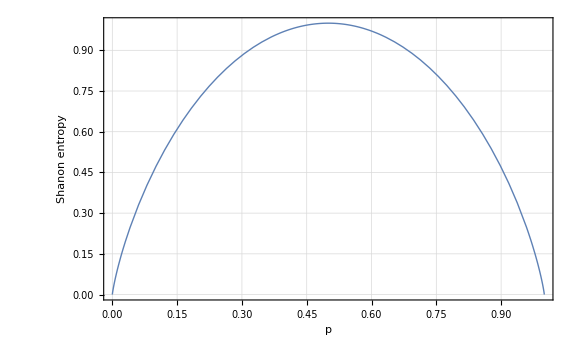

Figure 1. The Shannon entropy H({p,1−p}) associated with a binary probability distribution {p(0)=p,p(1)=1−p} of a random variable with values in {0,1}.

So far, entropy has been regarded as a measure of uncertainty. It may sound contradictory at first glance, but a valuable alternative interpretation is that entropy quantifies the information content in the state of a physical system. Suppose that we have learned value x of a random variable X. Compared to the case we did not learn the value, our knowledge of the random variable has increased. We then ask the question, “How much of information, on average, have we acquired by learning the value of X?” Since the Shannon entropy is the amount of uncertainty before we learn the value and it is the amount of uncertainty that is cleared by learning the value, the information gain is also given by the Shannon entropy. The two interpretations thus provide two alternative views of entropy: One can regard the entropy as a measure of the uncertainty before we learn the value of X. But one can also regard it as a measure of the information gained after we learn the value of X.

A basic yet significant property of the Shannon entropy is the inequality

0≤H(X)≤log d ,

where d is the number of values that X can take. The entropy becomes maximum, H(X)=log d, if and only if the probability is uniformly distributed. We defer proving the property until we introduce relative entropy since the proof is simplest by using this quantity.

Relative Entropy

The relative entropy (also known as Kullback-Leibler divergence) is a measure of the closeness of two probability distributions. In character, it is quite different from the previously introduced measures, the Euclidean distance, the Kolmogorov distance, or the classical fidelity. It behaves, in many respects, more like the entropy as the name suggests.

Suppose that {p(x)} and {q(x)} are two probability distributions of the same random variable X with values in {x}. The relative Shannon entropy or simply relative entropy of {p(x)} to {q(x)} (or the Kullback-Leibler divergence of {p(x)} from {q(x)}) is defined by

H({p(x)}∥{q(x)}):=Σ_x p(x) log (p(x))/(q(x))=-H({p(x)})-Σ_x p(x)logq(x).

As before, it is assumed that 0log0=0. In addition, we define p(x) log 0 = −∞ if p(x) > 0 for any x. In information theory, the second term, -∑_xp(x)logq(x), is often called the cross-entropy of two probability distributions {p(x)} and {q(x)}, and itself is used to measure the difference of two probability distributions.

Consider two probability distributions.

```mathematica
pp=Normalize[{1,3,1,5,3,4},Total]
```

{1/17,3/17,1/17,5/17,3/17,4/17}

```mathematica
qq=Normalize[{1,3,2,4,1,1},Total]
```

{1/12,1/4,1/6,1/3,1/12,1/12}

Calculate the (classical) relative entropy between the two probability distributions

```mathematica
rel=ShannonEntropy[pp,qq]
```

6/17+(5 Log[3])/(17 Log[2])-(5 Log[17/5])/(17 Log[2])-(4 Log[17/4])/(17 Log[2])-(6 Log[17/3])/(17 Log[2])+Log[6]/(17 Log[2])+(8 Log[12])/(17 Log[2])-(2 Log[17])/(17 Log[2])

```mathematica
rel//N
```

0.283648

Why is the relative entropy a good measure of closeness of two probability distributions? Or, is it at all? For example, consider the two probability distributions

{p(x)}={2/3,(1-ϵ)/3,ϵ/3},	    {q(x)}={2/3,1/3,0/3}

with 0<ϵ≤1. The two distributions look reasonably similar to each other. Yet, we have H({p(x)}∥{q(x)}) = ∞ for any arbitrarily small yet finite ϵ. For comparison, consider another probability distribution

{r(x)}={1/6,5/6,0}.

It looks considerably different from both {p(x)} and {q(x)}. However, we have

H({r(x)} ∥ {q(x)}) ≈ 1.4183.

Why should we regard that {p(x)} is more different from {q(x)} than {r(x)} is?

Another weird property of the relative entropy, as a distance measure, is that it is asymmetric about {p(x)} and {q(x)}. For the above example, we already observed

H({p(x)} ∥ {q(x)}) = ∞,

whereas we find

H({q(x)} ∥ {p(x)}) ≈ ϵ/(3log2)≈0.

Consider an evil dice with strongly biased probability distribution.

```mathematica
pp=Normalize[{1,2,2,4,3,0},Total]
```

{1/12,1/6,1/6,1/3,1/4,0}

Here is another probability distribution.

```mathematica
ϵ=1/100;
δ=Append[Table[-ϵ,5],5ϵ];
qq=pp+δ
```

{11/150,47/300,47/300,97/300,6/25,1/20}

The two probability distributions look similar. Indeed, the classical fidelity between them is reasonably high.

```mathematica
ClassicalFidelity[pp,qq]//N
```

0.974596

Nevertheless, the relative entropy of qq to pp diverges.

```mathematica
ShannonEntropy[qq,pp]
```

∞

Note that relative entropy is asymmetrical about the two input arguments, and the relative entropy of pp to qq is finite.

```mathematica
ShannonEntropy[pp,qq]//N
```

0.0744957

Because of the above drawbacks, the relative entropy is not particularly useful or interesting in its own right. There is a separate reason why it is used so broadly in investigating entropic quantities and relations. At the core of the reason is Gibbs’ inequality

H({p(x)} ∥ {q(x)}) ≥ 0

with equality attained if and only if the two probability distributions {p(x)} and {q(x)} are identical. A widely popular technique is to express entropic quantities in terms of the relative entropy or regard them as special cases of the relative entropy, and then use the Gibbs’ inequality as necessary.

As an example, let us prove that the maximum entropy is logd for a random variable X taking d distinct values, using Gibbs’ inequality. Let {p(x)} be the probability distribution associated with X. In addition, we consider a uniform distribution q(x)=1/d. According to Gibbs’ inequality, we have

H({p(x)} ∥ {q(x)}) = −H({p(x)}) + log d ≥ 0 .

The equality is attained if and only if p(x) is uniform just like q(x); that is, p(x)=1/d.

Let us close this subsection with a proof of Gibbs’ inequality. It is instructive because some of its elements are frequently used to study other entropic quantities and relations. We first recall the properties of a convex function. A function f(x) is said to be convex if it satisfies

f((1−t)x + ty)≤(1−t)f(x)+tf(y)

for all 0≤t≤1 and all x and y in the domain of the function. It is often expressed in a slightly more general but equivalent form

f(Σ_j p(j)x_j) ≤ Σ_j p(j)f(x_j)

for all x_j and all p(j) such that 0≤p(j)≤1 and Σ_j p(j)=1.If f(x) is differentiable, then one can express the convexity condition in the form

f(x)≥f(y)+f'(y)(x−y)

for all x and y. Geometrically, this means that the graph of f(x) lies above all its tangents. Now, note that f (x)=− logx is a convex function. Then, we apply the above condition to this negative logarithm function by putting y=1 to get

-logx≥(1-x)/(log_2 2) .

Finally, we examine the relative entropy and obtain

H({p(x)}∥{q(x)})=−Σ_xp(x)log(p(x))/(q(x))≥Σ_x p(x)(1-(q(x))/(p(x))) .

Then, it is clear that

H({p(x)} ∥ {q(x)})≥Σ_x(p(x)-q(x))=1-1=0 .

Mutual Information

So far, we have considered a single random variable. Let us now consider two random variables X and Y . Suppose that they randomly take values from the sets {x} and {y}, respectively, governed by the joint probability distribution p(x,y). As long as one is concerned with the total uncertainty in X and Y or the total information gain after one learns the both values of X and Y, there is nothing new. The quantity in question is nothing but the Shannon entropy associated with the joint probability distribution

H(X,Y )≡H({p(x, y)})=−Σ_(x,y)p(x,y)logp(x,y).

To distinguish it from other entropies to be introduced below, we call it joint Shannon entropy or simply joint entropy.

With multiple random variables, a more interesting question is, how much do we get to know about X (or how much our uncertainty in X still remains) when we have learned the value of Y? By learning the value of Y, the amount of information we acquire about X is the Shannon entropy,

H(Y ) = H({p(y)})

associated with the probability distribution of Y, p(y)=Σ_x p(x,y). In other words, the total uncertainty H(X,Y ) about X and Y has decreased by this same amount of uncertainty H(Y ). The Shannon entropy of X conditional on knowing Y or simply conditional entropy of X on Y,

H(X|Y ):=H(X,Y )−H(Y ),

is the amount of uncertainty still remaining about X given that we know the value of Y. One can further justify the above definition as a measure of conditional uncertainty. Initially, that is, before we learn the value of Y, the probability distribution of X is given by p(x) = Σ_x p(x, y). After we learn the value of Y , the random variable X is now governed by the conditional probability distribution p(x|y). Therefore, one can estimate the average amount of uncertainty about X still remaining after we know Y, H(X|Y ), by the Shannon entropy associated with the conditional probability distribution p(x|y),

H(X|Y )=⟨H({p(x|y)})⟩_Y ,

where the average is over all possible values of Y with respect to the probability
distribution p(y). By Bayes’ rule, the conditional probability is given by

p(x|y) =(p(y|x)p(x))/(p(y))=(p(x,y))/(p(y)) .

Then, we have

H(X|Y )=−Σ_yp(y)Σ_x(p(x,y))/(p(y))log(p(x,y))/(p(y))=-Σ_(x,y)p(x,y)logp(x,y)+Σ_y p(y)logp(y)=H(X,Y)-H(Y),

reproducing the previous defining expression.

If X and Y are statistically independent, then learning the value of Y does not help know about X at all. In this case, one thus expects that the remaining uncertainty H(X|Y ) after knowing Y is the same as the Shannon entropy H({p(x)}) associated with the initial probability distribution p(x) of X. This is indeed the case since with p(x,y)=p(x)p(y), we have H(X,Y )=H(X)+H(Y ) and hence H(X|Y )=H(X). On the other hand, if the two variables are correlated with each other, then learning the value of Y reduces the uncertainty about X, on average, below the initial level. For example, consider X and Y taking values from a common value set {1,2, …,6}. Suppose that p(x,y)=δ_(x,y)/6. Once the value of Y is known, we know the value of X with certainty and there remains no uncertainty about X.

Therefore, the difference between the initial amount of uncertainty about X and the amount of uncertainty about X remaining after learning the value of Y measures the correlation between the two variables. We call it the mutual information of X and Y , and denote it by H(X:Y ). In other words, the mutual information

H(X:Y ):=H(X)−H(X|Y ) ,

quantifies the common information shared by X and Y. From the definition of conditional entropy, we have identities

H(X:Y )=H(X)+H(Y )−H(X,Y )=H(X)−H(X|Y )= H(Y )−H(Y |X) .

Consider a classical joint probability distribution  p_(i j):=p(x_i,y_j) for i=1,2,… and j=1,2,… associated with two random variables X and Y.

```mathematica
pp=RandomReal[{0,1},{6,6}];
pp/=Total[Flatten@pp];
pp//MatrixForm
```

(0.0436355 | 0.0150827 | 0.0149903 | 0.0564177 | 0.00884432 | 0.00533618
0.0259039 | 0.0181305 | 0.0381321 | 0.0126118 | 0.0193132 | 0.0363682
0.00198824 | 0.0361224 | 0.0555776 | 0.00650371 | 0.0415962 | 0.0195236
0.00222343 | 0.0211931 | 0.0370593 | 0.0655215 | 0.0174594 | 0.0481294
0.0511113 | 0.00696398 | 0.0352387 | 0.0263186 | 0.00847998 | 0.0138094
0.0109489 | 0.0412931 | 0.0115375 | 0.0350049 | 0.058899 | 0.0527306)

The mutual information between the two variables is given as follows.

```mathematica
MutualInformation[pp]
```

0.29231

Consider two statistically independent random variables.

```mathematica
p=Normalize[RandomReal[{0,1},6],Total]
q=Normalize[RandomReal[{0,1},4],Total]
```

{0.280059,0.0302519,0.111875,0.227639,0.137607,0.212568}

{0.373748,0.061267,0.0155914,0.549393}

The joint probability is given by the dyadic product of the two probability distributions.

```mathematica
pq=Dyad[p,q];
pq//MatrixForm
```

(0.104672 | 0.0171584 | 0.00436652 | 0.153863
0.0113066 | 0.00185344 | 0.000471669 | 0.0166202
0.0418131 | 0.00685424 | 0.00174429 | 0.0614634
0.0850797 | 0.0139467 | 0.00354921 | 0.125063
0.0514304 | 0.00843077 | 0.00214549 | 0.0756004
0.0794468 | 0.0130234 | 0.00331423 | 0.116783)

The mutual information is expected to vanish.

```mathematica
MutualInformation[pq]//Chop
```

0

Now, consider two anti-correlated random variables.

```mathematica
pp=Normalize[RandomReal[{0,1},6],Total];
pp=Chop@Reverse@DiagonalMatrix@pp;
MatrixForm[pp]
```

(0 | 0 | 0 | 0 | 0 | 0.272785
0 | 0 | 0 | 0 | 0.105183 | 0
0 | 0 | 0 | 0.109621 | 0 | 0
0 | 0 | 0.233205 | 0 | 0 | 0
0 | 0.0673851 | 0 | 0 | 0 | 0
0.211821 | 0 | 0 | 0 | 0 | 0)

```mathematica
MutualInformation[pp]
```

2.42893

From the above arguments leading to the definition of mutual information, it is physically clear that the conditional entropy H(X|Y ) cannot exceed H(X) (see Problem 7.1 in the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7 for a mathematical proof). This implies the subadditivity

H(X, Y )≤H(X)+H(Y )

with equality if and only if X and Y are statistically independent. For the same reason, the mutual information H(X:Y ) cannot exceed H(X) nor H(Y ) (Problem 7.1 in the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7 for a mathematical proof),

H(X:Y )≤H(X),

which is equivalent to

H(X|Y )≥0.

Equality in each of the above two equations is attained if and only if X is a function of Y, X = f(Y ), that is, if X and Y are perfectly correlated. The inequality H(X:Y )≤H(X) is often called the data processing inequality.

Let us now demonstrate that classical mutual information cannot exceeds the Shannon entropies of two individual probability distributions.

Define a function randomly generate a joint probability distribution p(x,y) and then returns a pair {H(X:Y), H(Y)} of the mutual information and Shannon entropy .

```mathematica
try[]:=Block[
{pp=RandomReal[{0,1},{6,6}]},
pp/=Total[Flatten@pp];
{MutualInformation[pp],ShannonEntropy@Total@pp}
]
```

```mathematica
EchoTiming[data=Table[try[],20000];]
```

1.54291

```mathematica
max=Max[data];
ListPlot[data,Epilog->Line@{{0,0},{1,1}*max},PlotRange->{{0,1},{0,1}}*max,AspectRatio->1,FrameLabel->{"H(X:Y)","H(Y)"}]
```

-Graphics-

There are many more interesting and useful properties of entropies and mutual information. Here, we have kept the discussion minimal. Interested readers may refer to Wehrl (1978).

Data Compression

As an example of application of the Shannon entropy, let us consider a problem of data compression. Suppose that we have a binary string of of length n,

x_1 x_2(…x)_n

with each ‘character’ x_k∈{0,1}. Is it possible to compress the string into a shorter string that still carries the same information? If it is the case, one can save the physical resource, say, to store the message.

To mathematically model the problem, we regard each character x_k for k=1,2,…,n as a realization of a random variable X_k. We assume that the random variables X_k are statistically independent and identically distributed with the probabilities p(0)=p and p(1)=1−p.

The basic idea to compress the message is to classify strings into typical and atypical strings. For large n, a string such as 00… 0 or 11…1 is highly unlikely, and we regard it atypical. Typical strings contain, on average, np 0s and n(1−p) 1s. We do not need to store every string of characters. We only store typical strings. The probability for an actual string to be atypical vanishes for large n.

How many distinct typical strings are there then? Before we estimate the number N_typical of such strings, we first calculate the probability p(x_1,x_2,… ,x_n) for a particular typical string x_1 x_2(…x)_n. Since the characters are independent and identically distributed,

p(x_1,… ,x_n)=p(x_1)p(x_2)…p(x_n)≈(p^np(1-p))^(n(1-p)) ,

as long as x_1 x_2(…x)_n is a typical string. We observe that the probabilities to get different typical strings are uniform, independent of the string. This implies that N_typical=1/p(x_1,x_2,…,x_n). From the above equation, we then have

log N_typical≈-logp(x_1,x_2,…,x_n)=n[-plogp-(1-p)log(1-p)]=nH({p,1-p}) .

In short, there are 2^(nH({p,1−p})) typical strings. This implies that we only need nH ({p, 1 − p}) bits to store n-bit strings. We save n[1−H ({p,1−p})] bits. This is what Shannon’s noiseless coding theorem essentially states.

In the above argument, we have considered binary strings. It can be easily extended for an alphabet of d characters, {c_1,c_2,… ,c_d}. The random variables modeling different characters are statistically independent and governed by the same probability distribution {p(x) : x = c_2,c_2,…,c_d}. Typical strings contain np(x) xs for x=c_1,c_2,… ,c_d. The probability for a particular string is then given by

p(x_1,x_2,…,x_n)=Π_(k=1)^n p(x_k)≈Π_(x=c_1)^c_d(p(x))^(np(x))

as long as the string x_1 x_2(…x)_n is typical. Therefore, we have

log N_typical=-logp(x_1,x_2,…,x_n)=-n Σ_x p(x)logp(x)=nH({p(x)}) .

This implies that we need a physical resource to store only 2^(nH({p(x)})) instead of
all d^n strings.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Information Theory
▪Quantum Information Systems with Q3

| Related Links
▪A. Wehrl, Reviews of Modern Physics 50, 221 (1978)https://doi.org/10.1103/RevModPhys.50.221, “General properties of entropy.”
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).